# Resource-driven disease dynamics: linking resources, traits, trophic cascades, and instability using loop analysis

State Variables:
S => Susceptible host density
F (I) => Infected host density
Z => Propagule density
A => Algal resource density

Parameters: 
ds => loss rate, hosts
dz => loss rate, propagules
e => conversion efficiency
f => feeding rate, fixed slope or maximum
h => half-saturation constant, feeding rate
k1 => carrying capacity, algal resource
o => propagule yield, fixed slope or maximum
r => growth rate, algal resource
u => per propagule infectivity
v => virulent mortality
theta => reduction of feeding rate, infected hosts

### Initialization

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
Quiet[<<"/Users/eden/Desktop/RESEARCH/CODE/Dynamica/Dynamica.m"]
```

Dynamica (Version 1.0.11 - 5/8/2021), Copyright(c) 1993-2021 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

```mathematica
Quiet[<<"/Users/eden/Downloads/lce.m"]
```

## FIGURE 4

```mathematica
Clear[e,h,f,dz,u,v,o,theta,r,ds,k1]
```

```mathematica
dAT3 = r*A*(1 - A/k1)-((f*A)/(h^2+A^2))*A*(S+theta*F);
dST3= e*((f*A)/(h^2+A^2))*(S+theta*F)*A - ds*S - u*((f*A)/(h^2+A^2))*Z*S;
dFT3=u*((f*A)/(h^2+A^2))*Z*S - (ds + v)*F;
dZT3=o*(ds + v)*F - dz*Z - ((f*A)/(h^2+A^2))*(S+theta*F)*Z;
```

### Jacobian Elements & Feedbacks

```mathematica
J11T3 = FullSimplify[D[dAT3,A]];
J12T3 = FullSimplify[D[dAT3,S]];
J13T3 = FullSimplify[D[dAT3,F]];
J14T3 = FullSimplify[D[dAT3,Z]];
```

```mathematica
J21T3 = FullSimplify[D[dST3,A]];
J22T3 = FullSimplify[D[dST3,S]];
J23T3 = FullSimplify[D[dST3,F]];
J24T3 = FullSimplify[D[dST3,Z]];
```

```mathematica
J31T3 = FullSimplify[D[dFT3,A]];
J32T3 = FullSimplify[D[dFT3,S]];
J33T3 = FullSimplify[D[dFT3,F]];
J34T3 = FullSimplify[D[dFT3,Z]];
```

```mathematica
J41T3 = FullSimplify[D[dZT3,A]];
J42T3 = FullSimplify[D[dZT3,S]];
J43T3 = FullSimplify[D[dZT3,F]];
J44T3 = FullSimplify[D[dZT3,Z]];
```

```mathematica
JMT3 = {{J11T3,J12T3,J13T3,J14T3},{J21T3,J22T3,J23T3,J24T3},{J31T3,J32T3,J33T3,J34T3},{J41T3,J42T3,J43T3,J44T3}};
JMT3//MatrixForm
```

(r-(2 A r)/k1-(2 A f h^2 (S+F theta))/((A^2+h^2)^2) | -(A^2 f)/(A^2+h^2) | -(A^2 f theta)/(A^2+h^2) | 0
(2 A e f h^2 (S+F theta)+f (A-h) (A+h) S u Z)/((A^2+h^2)^2) | -(A^2 (ds-e f)+ds h^2+A f u Z)/(A^2+h^2) | (A^2 e f theta)/(A^2+h^2) | -(A f S u)/(A^2+h^2)
(f (-A^2+h^2) S u Z)/((A^2+h^2)^2) | (A f u Z)/(A^2+h^2) | -ds-v | (A f S u)/(A^2+h^2)
(f (A-h) (A+h) (S+F theta) Z)/((A^2+h^2)^2) | -(A f Z)/(A^2+h^2) | o (ds+v)-(A f theta Z)/(A^2+h^2) | -dz-(A f (S+F theta))/(A^2+h^2))

```mathematica
(* Make a dummy Jacobian *)
DJac = {{jAA,jAS,jAF,0},{jSA,jSS,jSF,jSZ},{jFA,jFS,jFF,jFZ},{jZA,jZS,jZF,jZZ}};
DJac//MatrixForm
```

(jAA | jAS | jAF | 0
jSA | jSS | jSF | jSZ
jFA | jFS | jFF | jFZ
jZA | jZS | jZF | jZZ)

```mathematica
CharacteristicPolynomial[DJac,x]
```

-jFZ (jAS jSF jZA-jAF jSS jZA-jAS jSA jZF+jAA jSS jZF+jAF jSA jZS-jAA jSF jZS+jAF jZA x-jAA jZF x-jSS jZF x+jSF jZS x+jZF x^2)+jSZ (jAS jFF jZA-jAF jFS jZA-jAS jFA jZF+jAA jFS jZF+jAF jFA jZS-jAA jFF jZS-jAS jZA x-jFS jZF x+jAA jZS x+jFF jZS x-jZS x^2)+(jZZ-x) (-jAS jFF jSA+jAF jFS jSA+jAS jFA jSF-jAA jFS jSF-jAF jFA jSS+jAA jFF jSS+jAF jFA x-jAA jFF x+jAS jSA x+jFS jSF x-jAA jSS x-jFF jSS x+jAA x^2+jFF x^2+jSS x^2-x^3)

#### Feedback Level 1

```mathematica
Tr[DJac]
```

jAA+jFF+jSS+jZZ

```mathematica
T3L1 = FullSimplify[(J11T3+J22T3+J33T3+J44T3)]
```

-ds-dz+r-(2 A r)/k1-(2 A f h^2 (S+F theta))/((A^2+h^2)^2)-(A f (S+F theta))/(A^2+h^2)-v-(A^2 (ds-e f)+ds h^2+A f u Z)/(A^2+h^2)

#### Feedback Level 2

```mathematica
T3L2 = FullSimplify[(J12T3*J21T3-J11T3*J22T3)+(J13T3*J31T3-J11T3*J33T3)+(-J11T3*J44T3)+(J23T3*J32T3-J22T3*J33T3)+(J24T3*J42T3-J22T3*J44T3)+(J34T3*J43T3-J33T3*J44T3)];
```

```mathematica
(* These are the L2 loops where J11 is involved *)
```

```mathematica
ConsResL2T3=FullSimplify[(J12T3*J21T3-J11T3*J22T3)+(J13T3*J31T3-J11T3*J33T3)+(-J11T3*J44T3)];
```

```mathematica
(* Spencer hypothesizes that these loops don't contribute much *)
EpidemL2T3 = FullSimplify[(J23T3*J32T3-J22T3*J33T3)+(J24T3*J42T3-J22T3*J44T3)+(J34T3*J43T3-J33T3*J44T3)];
```

#### Feedback Level 3

```mathematica
ASIT3L3 = -J11T3*(J23T3*J32T3-J22T3*J33T3)-J21T3*(J12T3*J33T3-J32T3*J13T3)-J31T3*(J13T3*J22T3-J23T3*J12T3);
```

```mathematica
ASZT3L3 =-J11T3*(J24T3*J42T3-J22T3*J44T3)-J21T3*(J12T3*J44T3)-J41T3*(-J24T3*J12T3);
```

```mathematica
AIZT3L3 = -J11T3*(J43T3*J34T3-J33T3*J44T3)-J31T3*(J13T3*J44T3)-J41T3*(-J13T3*J34T3);
```

```mathematica
SIZT3L3 = -J22T3*(J43T3*J34T3-J33T3*J44T3)-J32T3*(J23T3*J44T3-J43T3*J24T3)-J42T3*(J24T3*J33T3-J34T3*J23T3);
```

```mathematica
T3L3 = ASIT3L3+ASZT3L3+AIZT3L3+SIZT3L3;
```

#### Feedback Level 4

```mathematica
Det[DJac]
```

-jAS jFZ jSF jZA+jAF jFZ jSS jZA+jAS jFF jSZ jZA-jAF jFS jSZ jZA+jAS jFZ jSA jZF-jAA jFZ jSS jZF-jAS jFA jSZ jZF+jAA jFS jSZ jZF-jAF jFZ jSA jZS+jAA jFZ jSF jZS+jAF jFA jSZ jZS-jAA jFF jSZ jZS-jAS jFF jSA jZZ+jAF jFS jSA jZZ+jAS jFA jSF jZZ-jAA jFS jSF jZZ-jAF jFA jSS jZZ+jAA jFF jSS jZZ

```mathematica
T3L4 = Simplify[-(-J12T3*J34T3*J23T3*J41T3+J13T3*J34T3*J22T3*J41T3+J12T3*J33T3*J24T3*J41T3-J13T3*J32T3*J24T3*J41T3+J12T3*J34T3*J21T3*J43T3-J11T3*J34T3*J22T3*J43T3+J11T3*J32T3*J24T3*J43T3-J13T3*J34T3*J21T3*J42T3+J11T3*J34T3*J23T3*J42T3-J11T3*J33T3*J24T3*J42T3-J12T3*J33T3*J21T3*J44T3+J13T3*J32T3*J21T3*J44T3-J11T3*J32T3*J23T3*J44T3+J11T3*J33T3*J22T3*J44T3-
J12T3*J31T3*J24T3*J43T3+J13T3*J31T3*J24T3*J42T3+
J12T3*J31T3*J23T3*J44T3-J13T3*J31T3*J22T3*J44T3)];
```

#### Oscillation Criterion

```mathematica
UL2T3 = ((T3L1*T3L2+T3L3)*T3L3)/T3L1^2-T3L4;
```

### A

```mathematica
Clear[ds];
e = 8;
h = 0.2314;
f = 0.0153;
dz = 0.9;
u = 1.049;
v = 0.05157;
o = 483.8;
r = 1;
theta = 0.8;
ds=0.025;
```

```mathematica
solsT3 = Solve[{dST3==0,dFT3==0,dZT3==0,dAT3==0},{A,S,F,Z},WorkingPrecision->MachinePrecision];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
solsT3[[5]]/.{k1->3}
```

{A→0.43524+9.99201×10^-16 ⅈ,S→0.126173-5.09553×10^-13 ⅈ,F→38.8352+2.40473×10^-13 ⅈ,Z→819.771+4.98754×10^-12 ⅈ}

```mathematica
saddleT3 = solsT3[[5]]/.ds->0.025;(* evaluated at ds = 0.025*)
```

```mathematica
Show[
RegionPlot[0.11744 < x<1.214609,{x,0,4},{y,-40,40}, BoundaryStyle->{Purple},PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[x>1.214609,{x,0,4},{y,-40,40}, BoundaryStyle->{Gray},PlotStyle->{Yellow, Opacity[0.1]}],
Plot[Re[T3L1/.saddleT3/.ds->0.025],{k1,0,2.5}, PlotStyle->{Gray,Dashed}],
Plot[Re[T3L2/.saddleT3/.ds->0.025],{k1,0,2.5}, PlotStyle->{Gray,Dotted}],
Plot[Re[T3L3/.saddleT3/.ds->0.025],{k1,0,2.5},PlotStyle->Red],
Plot[Re[T3L4/.saddleT3/.ds->0.025],{k1,0,2.5}, PlotStyle->Gray],
Plot[Re[UL2T3/.saddleT3/.ds->0.025],{k1,0,2.5}, PlotStyle->{Blue,Dashed}],
Graphics[InfiniteLine[{{0,0},{5,0}}]],
PlotRange->{{0,2.5},{-34,20}},FrameTicks->{{{-30,-20,-10,0,10,20},None},{{0,0.5,1,1.5,2,2.5},None}},
AspectRatio->1,LabelStyle->{16, Black},AxesOrigin->{0,-34}
]
```

### B

```mathematica
Show[
RegionPlot[0.11744 < x<1.214609,{x,0,4},{y,-40,40}, BoundaryStyle->{Purple},PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[x>1.214609,{x,0,4},{y,-40,40}, BoundaryStyle->{Gray},PlotStyle->{Yellow, Opacity[0.1]}],
Plot[Re[ASIT3L3/.saddleT3/.ds->0.025],{k1,0,2.5}, PlotStyle->{Gray,Dashed}],
Plot[Re[ASZT3L3/.saddleT3/.ds->0.025],{k1,0,2.5}, PlotStyle->Red],
Plot[Re[AIZT3L3/.saddleT3/.ds->0.025],{k1,0,2.5}, PlotStyle->{Gray,Dotted}],
Plot[Re[SIZT3L3/.saddleT3/.ds->0.025],{k1,0,2.5}, PlotStyle->Gray],
Plot[Re[T3L3/.saddleT3/.ds->0.025],{k1,0,2.5},PlotStyle->{Blue,Dashed}],
Graphics[InfiniteLine[{{0,0},{5,0}}]],
PlotRange->{{0,2.5},{-10,12}},FrameTicks->{{{-10,-5,0,5,10},None},{{0,0.5,1,1.5,2,2.5},None}},
AspectRatio->1,LabelStyle->{Black,16},AxesOrigin->{0,-9}
]
```

### C

```mathematica
Show[
RegionPlot[0.11744 < x<1.214609,{x,0,4},{y,-40,40}, BoundaryStyle->{Purple},PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[x>1.214609,{x,0,4},{y,-40,40}, BoundaryStyle->{Gray},PlotStyle->{Yellow, Opacity[0.1]}],
Plot[Re[-J11T3*(J24T3*J42T3-J22T3*J44T3)/.saddleT3/.ds->0.025],{k1,0,2.5}, PlotStyle->Red],
Plot[Re[-J21T3*(J12T3*J44T3)/.saddleT3/.ds->0.025],{k1,0,2.5}, PlotStyle->{Gray,Dashed}],
Plot[Re[-J41T3*(-J24T3*J12T3)/.saddleT3/.ds->0.025],{k1,0,2.5}, PlotStyle->Gray],
Plot[Re[ASZT3L3/.saddleT3/.ds->0.025],{k1,0,2.5}, PlotStyle->{Blue, Dashed}],
Graphics[InfiniteLine[{{0,0},{5,0}}]],
PlotRange->{{0,2.5},{-10,12}},FrameTicks->{{{-10,-5,0,5,10},None},{{0,0.5,1,1.5,2,2.5},None}},
AspectRatio->1,LabelStyle->{Black,16},AxesOrigin->{0,-9}
]
```

### D

```mathematica
Show[
RegionPlot[0.11744 < x<1.214609,{x,0,4},{y,-40,40}, BoundaryStyle->{Purple},PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[x>1.214609,{x,0,4},{y,-40,40}, BoundaryStyle->{Gray},PlotStyle->{Yellow, Opacity[0.1]}],
Plot[Re[-J11T3*(J24T3*J42T3)/.saddleT3/.ds->0.025],{k1,0,2.5}, PlotStyle->Gray],
Plot[Re[-J11T3*(-J22T3*J44T3)/.saddleT3/.ds->0.025],{k1,0,2.5}, PlotStyle->{Red}],
Plot[Re[-J11T3*(J24T3*J42T3-J22T3*J44T3)/.saddleT3/.ds->0.025],{k1,0,2.5}, PlotStyle->{Blue,Dashed}],
Graphics[InfiniteLine[{{0,0},{5,0}}]],
PlotRange->{{0,2.5},{-10,12}},FrameTicks->{{{-10,-5,0,5,10},None},{{0,0.5,1,1.5,2,2.5},None}},
AspectRatio->1,LabelStyle->{16,Black},AxesOrigin->{0,-9}
]
```

### E

```mathematica
Show[
RegionPlot[0.11744 < x<1.214609,{x,0,4},{y,-40,40}, BoundaryStyle->{Purple},PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[x>1.214609,{x,0,4},{y,-40,40}, BoundaryStyle->{Gray},PlotStyle->{Yellow, Opacity[0.1]}],
Plot[Re[-J11T3*(-J22T3*J44T3)/.saddleT3/.ds->0.025],{k1,0,2.5}, PlotStyle->{Blue,Dashed}],
Plot[Re[J11T3/.saddleT3/.ds->0.025],{k1,0,2.5}, PlotStyle->{Red}],
Plot[Re[J22T3/.saddleT3/.ds->0.025],{k1,0,2.5}, PlotStyle->{Gray,Dashed}],
Plot[Re[J44T3/.saddleT3/.ds->0.025],{k1,0,2.5}, PlotStyle->{Gray}],
Graphics[InfiniteLine[{{0,0},{5,0}}]],
PlotRange->{{0,2.5},{-25,12}},FrameTicks->{{{-20,-15,-10,-5,0,5,10},None},{{0,0.5,1,1.5,2,2.5},None}},
AspectRatio->1,LabelStyle->{16,Black},AxesOrigin->{0,-25}
]
```

## FIGURE 5

```mathematica
Clear[e,h,f,dz,u,v,o,theta,r,ds,k1]
```

```mathematica
dASP = r*A*(1 - A/k1)-f*A*(S+theta*F);
dSSP= e*f*(S+theta*F)*A - ds*S - u*f*Z*S;
dFSP=u*f*Z*S - (ds + v)*F;
dZSP=o*f*A*(ds + v)*F - dz*Z - f*(S+theta*F)*Z;
```

### Jacobian Elements & Feedbacks

```mathematica
J11SP = FullSimplify[D[dASP,A]];
J12SP = FullSimplify[D[dASP,S]];
J13SP = FullSimplify[D[dASP,F]];
J14SP = FullSimplify[D[dASP,Z]];
```

```mathematica
J21SP = FullSimplify[D[dSSP,A]];
J22SP = FullSimplify[D[dSSP,S]];
J23SP = FullSimplify[D[dSSP,F]];
J24SP = FullSimplify[D[dSSP,Z]];
```

```mathematica
J31SP = FullSimplify[D[dFSP,A]];
J32SP = FullSimplify[D[dFSP,S]];
J33SP = FullSimplify[D[dFSP,F]];
J34SP = FullSimplify[D[dFSP,Z]];
```

```mathematica
J41SP = FullSimplify[D[dZSP,A]];
J42SP = FullSimplify[D[dZSP,S]];
J43SP = FullSimplify[D[dZSP,F]];
J44SP = FullSimplify[D[dZSP,Z]];
```

```mathematica
JMSP = {{J11SP,J12SP,J13SP,J14SP},{J21SP,J22SP,J23SP,J24SP},{J31SP,J32SP,J33SP,J34SP},{J41SP,J42SP,J43SP,J44SP}};
JMSP//MatrixForm
```

(r-(2 A r)/k1-f (S+F theta) | -A f | -A f theta | 0
e f (S+F theta) | -ds+A e f-f u Z | A e f theta | -f S u
0 | f u Z | -ds-v | f S u
f F o (ds+v) | -f Z | A f o (ds+v)-f theta Z | -dz-f (S+F theta))

```mathematica
pars = {e -> 8,h->0.2314,f->0.0153,dz->0.9,u->1.049,v->0.05157,o->483.8,r->1,theta->0.8,k1->3};
StabEP = {S->35.5275, F->25.928,Z->3.48174, A->0.417208};
SadEP = {S->44.854, F->16.4934, Z->1.75428,A->0.335566};
```

```mathematica
(* Make a dummy Jacobian *)
DJac = {{jAA,jAS,jAF,0},{jSA,jSS,jSF,jSZ},{0,jFS,jFF,jFZ},{jZA,jZS,jZF,jZZ}};
DJac//MatrixForm
```

(jAA | jAS | jAF | 0
jSA | jSS | jSF | jSZ
0 | jFS | jFF | jFZ
jZA | jZS | jZF | jZZ)

```mathematica
Clear[ds,k1];
e = 8;
h = 0.2314;
f = 0.0153;
dz = 0.9;
u = 1.049;
v = 0.05157;
o = 483.8;
r = 1;
theta = 0.8;
```

```mathematica
(* Find the Saddle Equilibrium *)
sols = Solve[{dSSP==0,dFSP==0,dZSP==0,dASP==0},{A,S,F,Z}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{A→0.,S→0.,F→0.,Z→0.},5,{A→1/(3.54589×10^24-2.11193×10^26 ds-1-1+4.27121×10^26 ds k1),S→1/1,F→1,Z→(32+1)/(-8.65227×10^37+10+1)}}
 |  |  |  |

```mathematica
sols[[3]]/.pars/.ds->0.03
```

{A→0.245098,S→60.0197,F→0.,Z→0.}

```mathematica
saddle = sols[[5]]/.pars;
stable = sols[[7]]/.pars;
stableSA = sols[[3]]/.pars;
```

#### Feedback Level 1

```mathematica
Tr[DJac]
```

jAA+jFF+jSS+jZZ

```mathematica
SPL1 = FullSimplify[(J11SP+J22SP+J33SP+J44SP)];
```

#### Feedback Level 2

```mathematica
SPL2 = FullSimplify[(J12SP*J21SP-J11SP*J22SP)+(J13SP*J31SP-J11SP*J33SP)+(J14SP*J41SP-J11SP*J44SP)+(J23SP*J32SP-J22SP*J33SP)+(J24SP*J42SP-J22SP*J44SP)+(J34SP*J43SP-J33SP*J44SP)];
```

#### Feedback Level 3

```mathematica
SPL3 =FullSimplify[((J12SP*J23SP*J31SP+J21SP*J32SP*J13SP)+
(J14SP*J24SP*J41SP+J21SP*J42SP*J14SP)+(J23SP*J34SP*J42SP+J32SP*J43SP*J24SP)+
(J14SP*J43SP*J31SP+J41SP*J34SP*J13SP)-
((J33SP+J44SP)*(J12SP*J21SP-J11SP*J22SP)+(J22SP+J44SP)*(J13SP*J31SP-J11SP*J33SP)+
(J33SP+J22SP)*(J14SP*J41SP-J11SP*J44SP)+
(J11SP+J44SP)*(J23SP*J32SP-J22SP*J33SP)+
(J33SP+J11SP)*(J24SP*J42SP-J22SP*J44SP)+
(J11SP+J22SP)*(J34SP*J43SP-J33SP*J44SP))+J11SP*J22SP*J33SP+
J11SP*J22SP*J44SP+
J22SP*J33SP*J44SP)];
```

#### Feedback Level 4

```mathematica
Det[DJac]
```

-jAS jFZ jSF jZA+jAF jFZ jSS jZA+jAS jFF jSZ jZA-jAF jFS jSZ jZA+jAS jFZ jSA jZF-jAA jFZ jSS jZF+jAA jFS jSZ jZF-jAF jFZ jSA jZS+jAA jFZ jSF jZS-jAA jFF jSZ jZS-jAS jFF jSA jZZ+jAF jFS jSA jZZ-jAA jFS jSF jZZ+jAA jFF jSS jZZ

```mathematica
SPL4 = FullSimplify[-1*(-J12SP*J34SP*J23SP*J41SP+J13SP*J34SP*J22SP*J41SP+J12SP*J33SP*J24SP*J41SP-J13SP*J32SP*J24SP*J41SP+J12SP*J34SP*J21SP*J43SP-J11SP*J34SP*J22SP*J43SP+J11SP*J32SP*J24SP*J43SP-J13SP*J34SP*J21SP*J42SP+J11SP*J34SP*J23SP*J42SP-J11SP*J33SP*J24SP*J42SP-J12SP*J33SP*J21SP*J44SP+J13SP*J32SP*J21SP*J44SP-J11SP*J32SP*J23SP*J44SP+J11SP*J33SP*J22SP*J44SP)];
```

### A

```mathematica
FCNT3
```

FCNT3

### B (Time Series)

```mathematica
Clear[ds];
e = 8;
h = 0.2314;
f = 0.0153;
dz = 0.9;
u = 1.049;
v = 0.05157;
o = 483.8;
r = 1;
k1=3;
theta = 0.8;
```

```mathematica
Clear[ds,k1]
ds = 0.025;
Parat3x=ParametricNDSolveValue[{S'[t]== e*f*(S[t]+theta*F[t])*A[t] - ds*S[t] - u*f*Z[t]*S[t],
F'[t]==u*f*Z[t]*S[t] - (ds + v)*F[t],
Z'[t]==(o*f*A[t])*(ds + v)*F[t] - dz*Z[t] - f*(S[t]+theta*F[t])*Z[t],
A'[t] == r*A[t]*(1 - A[t]/k1)-f*A[t]*(S[t]+theta*F[t]),
S[0]==11.17,F[0]==0,Z[0]==0, A[0]==0.325,
WhenEvent[t==650,Z[t]->10]},{S,F,Z,A},{t,0,6000},{k1}];
Manipulate[
Show[LogPlot[Evaluate[#[t]& /@Parat3x[k1]],{t,0,5700},PlotRange->{{500,1200},{0.01,1000}},
 PlotStyle->{{Blue,Thick}, {Red,Thick},{Gray,Thick},{Darker[Green],Thick}},
PlotLegends->{"Susceptible","Infected","Spores","Algae","R"},TicksStyle->10,AspectRatio->1/2, LabelStyle->24, Frame->True, FrameLabel->{"","Log Concentration"}, FrameStyle->Black, FrameTicks->{{{0.1,{1.0,"1.0"},{10.0,"10.0"},{100.0,"100.0"},{1000.0,"1000.0"}},None},{{},None}},ImageSize->Large],
Graphics[{Directive[Dashed,Thick, Darker[Gray]],InfiniteLine[{{650,0},{650,5}}]}]],
{{k1,4},1,8}]
```

```mathematica
Parat3x2=ParametricNDSolveValue[{S'[t]== e*f*(S[t]+theta*F[t])*A[t] - ds*S[t] - u*f*Z[t]*S[t],
F'[t]==u*f*Z[t]*S[t] - (ds + v)*F[t],
Z'[t]==(o*f*A[t])*(ds + v)*F[t] - dz*Z[t] - f*(S[t]+theta*F[t])*Z[t],
A'[t] == r*A[t]*(1 - A[t]/k1)-f*A[t]*(S[t]+theta*F[t]),
S[0]==11.17,F[0]==0,Z[0]==0, A[0]==0.325,
WhenEvent[t==650,Z[t]->100]},{S,F,Z,A},{t,0,6000},{k1}];
Manipulate[
Show[LogPlot[Evaluate[#[t]& /@Parat3x2[k1]],{t,0,5700},PlotRange->{{500,1200},{0.01,1000}},
 PlotStyle->{{Blue,Thick}, {Red,Thick},{Gray,Thick},{Darker[Green],Thick}},
PlotLegends->{"Susceptible","Infected","Spores","Algae","R"},TicksStyle->10,AspectRatio->1/2, LabelStyle->24, Frame->True, FrameLabel->{"Time","Log Population Density (m/L)"},FrameTicks->{{{0.1,{1.0,"1.0"},{10.0,"10.0"},{100.0,"100.0"},{1000.0,"1000.0"}},None},{{{500,"0"},{600,"100"},{700,"200"},{800,"300"},{900,"400"},{1000,"500"},{1100,"600"},{1200,"700"}},None}}, FrameStyle->Black, ImageSize->Large],
Graphics[{Directive[Dashed,Thick, Darker[Gray]],InfiniteLine[{{650,0},{650,5}}]}]],
{{k1,4},1,8}]
```

### Population Plots (C & D)

```mathematica
AstarSPstab=sols[[7]][[1]][[2]];
SstarSPstab = sols[[7]][[2]][[2]];
FstarSPstab = sols[[7]][[3]][[2]];
AstarSPstabSA=sols[[3]][[1]][[2]];
SstarSPstabSA = sols[[3]][[2]][[2]];
FstarSPstabSA = sols[[3]][[3]][[2]];
AstarSPsad=sols[[5]][[1]][[2]];
SstarSPsad = sols[[5]][[2]][[2]];
FstarSPsad = sols[[5]][[3]][[2]];
```

```mathematica
Clear[ds];
e = 8;
h = 0.2314;
f = 0.0153;
dz = 0.9;
u = 1.049;
v = 0.05157;
o = 483.8;
r = 1;
theta = 0.8;
k1=3;
```

```mathematica
P1SP = Show[
Plot[Re[AstarSPsad]*10,{ds,0.02448898,0.03127101673}, PlotStyle->Darker[Green],AspectRatio->1,LabelStyle->16],
Plot[Re[SstarSPsad],{ds,0.02448898,0.03127101673}, PlotStyle->{Red,Dashed},AspectRatio->1,LabelStyle->16],
Plot[Re[FstarSPsad],{ds,0.02448898,0.03127101673}, PlotStyle->{Red, Dotted},AspectRatio->1,LabelStyle->16],
Plot[Re[SstarSPsad]+Re[FstarSPsad],{ds,0.02448898,0.03127101673}, PlotStyle->Red,AspectRatio->1,LabelStyle->16],
RegionPlot[0.02448898 < x <0.031271016,{x,0,0.14},{y,-10,100}, BoundaryStyle->{Black,Thick},PlotStyle->{Purple, Opacity[0.1]}],
Graphics[{Red,Thick,InfiniteLine[{{0.03127,0},{0.03127,5}}]}],
Graphics[InfiniteLine[{{0,0},{5,0}}]],
PlotRange->{{0.02448898,0.0312710167340415},{1,70}},
Frame->True,FrameLabel->{"Host Death Rate (d_s)","Population Density (S; m/L)"}, FrameTicks->{{{0,10,20,30,40,50,60,70},None},{{{0.025,"0.025"},{0.028,"0.028"},{0.031,"0.031"}},None}},LabelStyle->{Black,16},ImageSize->Medium
]
{{{0.025,"0.025"},{0.028,"0.028"},{0.031,"0.031"}},None}
```

{{{0.025,0.025},{0.028,0.028},{0.031,0.031}},None}

```mathematica
ASP = Show[
RegionPlot[0.024 < x <0.02448898 ,{x,0.02,0.03},{y,-10,100},BoundaryStyle->None, PlotStyle->Lighter[LightBlue]],
RegionPlot[0.031271016 < x <0.0316 ,{x,0.02,0.04},{y,-10,100},BoundaryStyle->None,PlotStyle->Lighter[Red,0.9]],
RegionPlot[0.02448898 < x <0.031271016,{x,0,0.14},{y,-10,100}, BoundaryStyle->{Black},PlotStyle->Lighter[Purple,0.9]],
Plot[Re[AstarSPstab],{ds,0.02448898,0.0316}, PlotStyle->Red,AspectRatio->1,LabelStyle->16],
Plot[Re[AstarSPsad],{ds,0.02448898,0.03127101673}, PlotStyle->{Dashed,Purple},AspectRatio->1,LabelStyle->16],
Plot[Re[AstarSPstabSA],{ds,0.024,0.03127101673}, PlotStyle->Blue,AspectRatio->1,LabelStyle->16],
Graphics[{Thick,Red,InfiniteLine[{{0.03127,0},{0.03127,5}}]}],
PlotRange->{{0.024,0.0316},{0.1,0.6}},AxesOrigin->{0,0},
Frame->True,FrameLabel->{"Host Death Rate (d_s)","Population Density (A)"},FrameTicks->{{{0.1,0.2,0.3,0.4,0.5,0.6},None},{{{0.025,"0.025"},{0.028,"0.028"},{0.031,"0.031"}},None}}, LabelStyle->{Black,16},ImageSize->Medium
];
SSP = Show[
RegionPlot[0.024 < x <0.02448898 ,{x,0.02,0.03},{y,-10,100},BoundaryStyle->None, PlotStyle->Lighter[LightBlue]],
RegionPlot[0.031271016 < x <0.0316 ,{x,0.02,0.04},{y,-10,100},BoundaryStyle->None,PlotStyle->Lighter[Red,0.9]],
RegionPlot[0.02448898 < x <0.031271016,{x,0,0.14},{y,-10,100}, BoundaryStyle->{Black},PlotStyle->Lighter[Purple,0.9]],
Plot[Re[SstarSPstab],{ds,0.02448898,0.0316}, PlotStyle->Red,AspectRatio->1,LabelStyle->16],
Plot[Re[SstarSPsad],{ds,0.02448898,0.03127101673}, PlotStyle->{Dashed,Purple},AspectRatio->1,LabelStyle->16],
Plot[Re[SstarSPstabSA],{ds,0.024,0.03127101673}, PlotStyle->Blue,AspectRatio->1,LabelStyle->16],
Graphics[{Red,Thick,InfiniteLine[{{0.03127,0},{0.03127,5}}]}],
PlotRange->{{0.024,0.0316},{20,70}},AxesOrigin->{0,0},
Frame->True,FrameLabel->{"Host Death Rate (d_s)","Population Density (S)"},FrameTicks->{{{20,30,40,50,60,70},None},{{{0.025,"0.025"},{0.028,"0.028"},{0.031,"0.031"}},None}}, LabelStyle->{Black,16},ImageSize->Medium
];
FSP = Show[
Plot[Re[FstarSPstab],{ds,0.02448898,0.03127101673}, PlotStyle->Red,AspectRatio->1,LabelStyle->16],
Plot[Re[FstarSPsad],{ds,0.02448898,0.03127101673}, PlotStyle->{Dashed,Purple},AspectRatio->1,LabelStyle->16],
Plot[Re[FstarSPstabSA],{ds,0.02448898,0.03127101673}, PlotStyle->Darker[Green],AspectRatio->1,LabelStyle->16],
RegionPlot[0.02448898 < x <0.031271016,{x,0,0.14},{y,-10,100}, BoundaryStyle->{Black,Thick},PlotStyle->{Purple, Opacity[0.1]}],
Graphics[{Red,Thick,InfiniteLine[{{0.03127,0},{0.03127,5}}]}],
PlotRange->{{0.02448898,0.0312710167340415},{1,40}},AxesOrigin->{0,0},
Frame->True,FrameLabel->{"Host Death Rate (d_s)","Population Density (I)"}, LabelStyle->{Black,16},ImageSize->Large
];
SFSP = Show[
Plot[Re[SstarSPstab + FstarSPstab],{ds,0.02448898,0.03127101673}, PlotStyle->Red,AspectRatio->1,LabelStyle->16],
Plot[Re[SstarSPsad + FstarSPsad],{ds,0.02448898,0.03127101673}, PlotStyle->{Dashed,Purple},AspectRatio->1,LabelStyle->16],
Plot[Re[SstarSPstabSA + FstarSPstabSA],{ds,0.02448898,0.03127101673}, PlotStyle->Darker[Green],AspectRatio->1,LabelStyle->16],
RegionPlot[0.02448898 < x <0.031271016,{x,0,0.14},{y,-10,100}, BoundaryStyle->{Black,Thick},PlotStyle->Lighter[Purple,0.8]],
Graphics[{Red,Thick,InfiniteLine[{{0.03127,0},{0.03127,5}}]}],
PlotRange->{{0.02448898,0.0312710167340415},{59,62}},AxesOrigin->{0,0},
Frame->True,FrameLabel->{"Host Death Rate (d_s)","Population Density (H; S+I)"}, LabelStyle->{Black,16},ImageSize->Large
];
```

```mathematica
ASP
```

```mathematica
SSP
```

### G, H, I

```mathematica
comp1SP = FullSimplify[-J11SP*(-J22SP*(J34SP*J43SP-J33SP*J44SP)-J32SP*(J23SP*J44SP-J43SP*J24SP)-J42SP*(J24SP*J33SP-J34SP*J23SP))];
comp2SP = FullSimplify[-J21SP*J12SP*(J43SP*J34SP-J33SP*J44SP)];
comp3SP = FullSimplify[-J21SP*J32SP*(J13SP*J44SP)];
comp4SP = FullSimplify[-J21SP*J42SP*(-J34SP*J13SP)];
comp5SP = FullSimplify[-J41SP*J24SP*(J12SP*J33SP-J32SP*J13SP)];
comp6SP = FullSimplify[-J41SP*J34SP*(J13SP*J22SP-J23SP*J12SP)];
```

```mathematica
Clear[ds]
e = 8;
h = 0.2314;
f = 0.0153;
dz = 0.9;
u = 1.049;
v = 0.05157;
o = 483.8;
r = 1;
k1=3;
theta = 0.8;
```

```mathematica
saddlecompplots = Show[
RegionPlot[0.024 < x <0.02448898 ,{x,0.02,0.03},{y,-10,100},BoundaryStyle->None, PlotStyle->Lighter[LightBlue]],
RegionPlot[0.031271016 < x <0.0316 ,{x,0.02,0.04},{y,-10,100},BoundaryStyle->None,PlotStyle->Lighter[Red,0.9]],
RegionPlot[0.02448898 < x <0.031271016,{x,0,0.14},{y,-10,100}, BoundaryStyle->{Black},PlotStyle->Lighter[Purple,0.9]],
Plot[comp5SP/.saddle,{ds,0.02448898,0.03127102},PlotStyle->Red,PlotPoints->10000],
Plot[comp6SP/.saddle,{ds,0.02448898,0.03127102},PlotStyle->Blue,PlotPoints->10000],
Plot[comp1SP+comp2SP+comp3SP+comp4SP/.saddle,{ds,0.02448898,0.03127102}, PlotStyle->Gray, PlotPoints->10000],
Plot[comp1SP+comp2SP+comp3SP+comp4SP+comp5SP+comp6SP/.saddle,{ds,0.02448898,0.03127102}, PlotStyle->Black, PlotPoints->100000],
Graphics[{Red,Thick,InfiniteLine[{{0.03127,0},{0.03127,5}}]}],
PlotRange->{{0.024,0.0316},{-0.011,0.011}},LabelStyle->{16,Black}, Frame->True, FrameLabel->{"Host Death Rate (d_s)",""},FrameTicks->{{{{-0.01,"-0.01"},{0.000,"0.000"},{0.01,"0.01"}},None},{{{0.025,"0.025"},{0.028,"0.028"},{0.031,"0.031"}},None}},AxesOrigin->{0.02448898,0}, AspectRatio->1, ImageSize->Medium];
```

```mathematica
stabSIZAcompplots = Show[
RegionPlot[0.024 < x <0.02448898 ,{x,0.02,0.03},{y,-10,100},BoundaryStyle->None, PlotStyle->Lighter[LightBlue]],
RegionPlot[0.031271016 < x <0.0316 ,{x,0.02,0.04},{y,-10,100},BoundaryStyle->None,PlotStyle->Lighter[Red,0.9]],
RegionPlot[0.02448898 < x <0.031271016,{x,0,0.14},{y,-10,100}, BoundaryStyle->{Black},PlotStyle->Lighter[Purple,0.9]],
Plot[comp5SP/.stable,{ds,0.02448898,0.03127102},PlotStyle->Red,PlotPoints->10000],
Plot[comp6SP/.stable,{ds,0.02448898,0.03127102},PlotStyle->Blue],
Plot[comp1SP+comp2SP+comp3SP+comp4SP/.stable,{ds,0.02448898,0.03127102}, PlotStyle->Gray],
Plot[comp1SP+comp2SP+comp3SP+comp4SP+comp5SP+comp6SP/.stable,{ds,0.02448898,0.03127102}, PlotStyle->Black,PlotPoints->10000],
Graphics[{Red,Thick,InfiniteLine[{{0.03127,0},{0.03127,5}}]}],
PlotRange->{{0.024,0.0316},{-0.011,0.011}},LabelStyle->{16,Black}, Frame->True, FrameLabel->{"",""},
FrameTicks->{{{{-0.01,"-0.01"},{0.000,"0.000"},{0.01,"0.01"}},None},{{{0.025,"0.025"},{0.028,"0.028"},{0.031,"0.031"}},None}},AxesOrigin->{0.02448898,0}, AspectRatio->1,ImageSize->Medium];
```

```mathematica
stabSAcompplots = Show[
RegionPlot[0.024 < x <0.02448898 ,{x,0.02,0.03},{y,-10,100},BoundaryStyle->None, PlotStyle->Lighter[LightBlue]],
RegionPlot[0.031271016 < x <0.0316 ,{x,0.02,0.04},{y,-10,100},BoundaryStyle->None,PlotStyle->Lighter[Red,0.9]],
RegionPlot[0.02448898 < x <0.031271016,{x,0,0.14},{y,-10,100}, BoundaryStyle->{Black},PlotStyle->Lighter[Purple,0.9]],
Plot[comp5SP/.stableSA,{ds,0.02448898,0.03127102},PlotStyle->Red],
Plot[comp6SP/.stableSA,{ds,0.02448898,0.03127102},PlotStyle->Blue],
Plot[comp1SP+comp2SP+comp3SP+comp4SP/.stableSA,{ds,0.02448898,0.03127102}, PlotStyle->Gray],
Plot[comp1SP+comp2SP+comp3SP+comp4SP+comp5SP+comp6SP/.stableSA,{ds,0.02448898,0.03127102}, PlotStyle->Black],
Graphics[{Red,Thick,InfiniteLine[{{0.03127,0},{0.03127,5}}]}],
PlotRange->{{0.024,0.0316},{-0.011,0.011}},LabelStyle->{16,Black}, Frame->True, FrameLabel->{"","Feedback Value"},FrameTicks->{{{{-0.01,"-0.01"},{0.000,"0.000"},{0.01,"0.01"}},None},{{{0.025,"0.025"},{0.028,"0.028"},{0.031,"0.031"}},None}},AxesOrigin->{0.02448898,0}, AspectRatio->1, ImageSize->Large];
```

```mathematica
stabSAcompplots
```

```mathematica
saddlecompplots
```

```mathematica
stabSIZAcompplots
```

## FIGURE 6

### A

```mathematica
T3SPFC
```

### B

```mathematica
Clear[ds,k1]
e = 8;
h = 0.2314;
f = 0.0153;
dz = 0.9;
u = 1.049;
v = 0.05157;
o = 483.8;
r = 1;
theta = 0.8;
ds = 0.0675;
Parat3xx=ParametricNDSolveValue[{S'[t]== e*((f*A[t])/(h^2+A[t]^2))*(S[t]+theta*F[t])*A[t] - ds*S[t] - u*((f*A[t])/(h^2+A[t]^2))*Z[t]*S[t],
F'[t]==u*((f*A[t])/(h^2+A[t]^2))*Z[t]*S[t] - (ds + v)*F[t],
Z'[t]==(o*((f*A[t])/(h^2+A[t]^2))*A[t])*(ds + v)*F[t] - dz*Z[t] - ((f*A[t])/(h^2+A[t]^2))*(S[t]+theta*F[t])*Z[t],
A'[t] == r*A[t]*(1 - A[t]/k1)-((f*A[t])/(h^2+A[t]^2))*A[t]*(S[t]+theta*F[t]),
S[0]==14.613885474268637,F[0]==29.472241702579876,Z[0]==18.043242307597435, A[0]==1.1597878385027218,
WhenEvent[t==650,A[t]->0.5]},{S,F,Z,A},{t,0,6000},{k1}];
Manipulate[
Show[LogPlot[Evaluate[#[t]& /@Parat3xx[k1]],{t,0,5500},PlotRange->{{600,800},{0.1,100}}, PlotStyle->{{Blue,Thick}, {Red,Thick},{Gray,Thick},{Darker[Green],Thick}},PlotLegends->{"Susceptible","Infected","Spores","Algae","R"},TicksStyle->10,AspectRatio->1, LabelStyle->16, Frame->True, FrameLabel->{"Time","Log Population Density (m/L)"},FrameTicks->{{{{0.1,"0.1"},{1.0,"1.0"},{10.0,"10.0"},{100.0,"100.0"}},None},{{{600,"0"},{700,"100"},{800,"200"}},None}}, FrameStyle->Black],
Graphics[{Directive[Dashed,Thick, Darker[Gray]],InfiniteLine[{{650,0},{650,5}}]}]],
{{k1,2.5},1,8}]
```

```mathematica
ds = 0.035;
Parat3xx2=ParametricNDSolveValue[{S'[t]== e*((f*A[t])/(h^2+A[t]^2))*(S[t]+theta*F[t])*A[t] - ds*S[t] - u*((f*A[t])/(h^2+A[t]^2))*Z[t]*S[t],
F'[t]==u*((f*A[t])/(h^2+A[t]^2))*Z[t]*S[t] - (ds + v)*F[t],
Z'[t]==(o*((f*A[t])/(h^2+A[t]^2))*A[t])*(ds + v)*F[t] - dz*Z[t] - ((f*A[t])/(h^2+A[t]^2))*(S[t]+theta*F[t])*Z[t],
A'[t] == r*A[t]*(1 - A[t]/k1)-((f*A[t])/(h^2+A[t]^2))*A[t]*(S[t]+theta*F[t]),
S[0]==14.613885474268637,F[0]==0,Z[0]==0, A[0]==1.1597878385027218,
WhenEvent[t==650,Z[t]->100]},{S,F,Z,A},{t,0,6000},{k1}];
```

```mathematica
Manipulate[
Show[LogPlot[Evaluate[#[t]& /@Parat3xx2[k1]],{t,0,5500},PlotRange->{{600,800},{0.01,100}}, PlotStyle->{{Blue,Thick}, {Red,Thick},{Gray,Thick},{Darker[Green],Thick}},PlotLegends->{"Susceptible","Infected","Spores","Algae","R"},TicksStyle->10,AspectRatio->1, LabelStyle->16, Frame->True, FrameLabel->{"Time","Log Population Density (m/L)"},FrameTicks->{{{{0.1,"0.1"},{1.0,"1.0"},{10.0,"10.0"},{100.0,"100.0"}},None},{{{600,"0"},{700,"100"},{800,"200"},{900,"300"}},None}}, FrameStyle->Black],
Graphics[{Directive[Dashed,Thick, Darker[Gray]],InfiniteLine[{{650,0},{650,5}}]}]],
{{k1,3.5},1,8}]
```

### C

Values of k in Figure:
2.5: Baseline Oscillations
3.5: Period Doubled
3.85: Chaos

```mathematica
Clear[ds,k1]
e = Rationalize[8];
h = Rationalize[0.2314];
f = Rationalize[0.0153];
ds = Rationalize[0.035];
dz = Rationalize[0.9];
u = Rationalize[1.049];
v = Rationalize[0.05157];
o = Rationalize[483.8];
theta = Rationalize[0.8];
r = Rationalize[1];
Parat3=ParametricNDSolveValue[{S'[t]== e*((f*A[t])/(h^2+A[t]^2))*(S[t]+theta*F[t])*A[t] - ds*S[t] - u*((f*A[t])/(h^2+A[t]^2))*Z[t]*S[t],
F'[t]==u*((f*A[t])/(h^2+A[t]^2))*Z[t]*S[t] - (ds + v)*F[t],
Z'[t]==(o*((f*A[t])/(h^2+A[t]^2))*A[t])*(ds + v)*F[t] - dz*Z[t] - ((f*A[t])/(h^2+A[t]^2))*(S[t]+theta*F[t])*Z[t],
A'[t] == r*A[t]*(1 - A[t]/k1)-((f*A[t])/(h^2+A[t]^2))*A[t]*(S[t]+theta*F[t]),
S[0]==11.17,F[0]==0,Z[0]==10, A[0]==0.325},{S,F,Z,A},{t,0,6000},{k1}];
Manipulate[
Show[LogPlot[Evaluate[#[t]& /@Parat3[k1]],{t,0,5500},PlotRange->{{4200,4600},{0.01,100}}, PlotStyle->{{Blue,Thick}, {Red,Thick},{Gray,Thick},{Darker[Green],Thick}},PlotLegends->{"Susceptible","Infected","Spores","Algae","R"},TicksStyle->10,AspectRatio->1/3, LabelStyle->12, Frame->True, FrameLabel->{"Time","Log Population Density (m/L)"},FrameTicks->{{{{0.1,"0.1"},{1.0,"1.0"},{10.0,"10.0"},{100.0,"100.0"}},None},{{{4200,"0"},{4400,"200"},{4600,"400"},{4800,"600"},{5000,"800"}},None}}, FrameStyle->Black, ImageSize->Medium]],
{{k1,3.85},1,8}]
```

### D

#### Lyapunov Exponent

```mathematica
Clear[e,h,f,dz,u,v,o,theta,r,ds,k1]
```

```mathematica
LEDS= DynamicalSystem[{
e*((f*A)/(h^2+A^2))*(S+theta*F)*A - ds*S - u*((f*A)/(h^2+A^2))*Z*S,
u*((f*A)/(h^2+A^2))*Z*S - (ds + v)*F,

(o*((f*A)/(h^2+A^2))*A)*(ds + v)*F - dz*Z - ((f*A)/(h^2+A^2))*(S+theta*F)*Z,
r*A*(1 - A/k)-((f*A)/(h^2+A^2))*A*(S+theta*F)
},
{{S,-0.1,200},{F,-0.1,200},{Z,-0.1,200},{A,-0.01,10}},
{{e,0,1000},{h,0,1},{f,0,1},{ds,0.001,0.1},{dz,0,1},{u,0,2},{v,0,0.2},{o,0,1000000},{theta,0,2},{r,0,2},{k,0.01,6}}]
```

DynamicalSystem[«4 ODEs»,{S,F,Z,A},{e,h,f,ds,dz,u,v,o,theta,r,k}]

```mathematica
LEt3 =  LEDS/.{e->Rationalize[8],h -> Rationalize[0.2314], f->Rationalize[0.0153], ds->Rationalize[0.035],dz->Rationalize[0.9], u->Rationalize[1.049], v->Rationalize[0.05157], o->Rationalize[483.8], theta->Rationalize[0.8], r->Rationalize[1],k->Rationalize[3.85]}
```

DynamicalSystem[«4 ODEs»,{S,F,Z,A},{ds→7/200,dz→9/10,e→8,f→153/10000,h→1157/5000,k→77/20,o→2419/5,r→1,theta→4/5,u→1049/1000,v→5157/100000}]

```mathematica
DisplayTrajectories[LEt3,{{11.7,0,100,0.325}},50000,MaxSteps->200000, PlotRange->All, BoxRatios->{1, 1, 1}];
```

NDSolve::mxst: Maximum number of 200000 steps reached at the point t == 40712.7.

```mathematica
P=Last[First[$Trajectories]]
```

{11.4082,19.1108,3.17741,0.219614}

```mathematica
Rationalize[P,0.0001]
```

{559/49,5523/289,197/62,29/132}

```mathematica
T1=Trajectory[LEt3,Rationalize[P,0.0000000001],15000, MaxSteps->Infinity,WorkingPrecision->24];
T2=Trajectory[LEt3,Rationalize[P+10^-9,0.0000000001],15000,MaxSteps->Infinity,WorkingPrecision->24];
```

$Aborted

```mathematica
dist=Table[{t,Log[EuclideanDistance[First[{S[t],F[t],Z[t],A[t]}/.T1],First[{S[t],F[t],Z[t],A[t]}/.T2]]]},{t,0,15000,0.1}];
```

```mathematica
Fit[Take[dist,40000],{1,t},t]
```

-18.3344+0.00472629 t

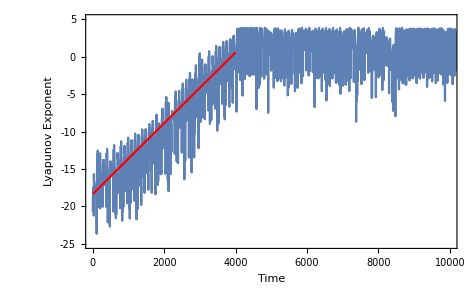

```mathematica
Show[ListPlot[dist,Joined->True,Frame->True, PlotRange->All],Plot[-18.334446137894325+0.0047262874907742 t,{t,0,4000},PlotStyle->Red], LabelStyle->{Black,20}, Frame->True,ImageSize->Medium,
 FrameLabel->{"Time", "Lyapunov Exponent"},FrameTicks->{{{{-25,"-25"},{-20,"-20"},{-15,"-15"},{-10,"-10"},{-5,"-5"},{0,"0"},{5,"5"}},None},{{{0,"0"},{2000,"2000"},{4000,"4000"},{6000,"6000"},{8000,"8000"},{10000,"10000"}},None}}, PlotRange->{{0,10000},{-25,5}}]
```

Larger exponent means faster spread on the attractor (positive exponent is chaotic)
Slope is the greatest exponent
Upper bound is the diameter of the attractor

#### Plot Chaotic Attractor

```mathematica
e = Rationalize[8];
h = Rationalize[0.2314];
f = Rationalize[0.0153];
ds = Rationalize[0.035];
dz = Rationalize[0.9];
u = Rationalize[1.049];
v = Rationalize[0.05157];
o = Rationalize[483.8];
theta = Rationalize[0.8];
r = Rationalize[1];
k1 = Rationalize[3.85];
```

```mathematica
T3SIZA[{S_,F_,Z_,A_}] := {e*((f*A)/(h^2+A^2))*(S+theta*F)*A - ds*S - u*((f*A)/(h^2+A^2))*Z*S,
u*((f*A)/(h^2+A^2))*Z*S - (ds + v)*F,
(o*((f*A)/(h^2+A^2))*A)*(ds + v)*F - dz*Z - ((f*A)/(h^2+A^2))*(S+theta*F)*Z,
r*A*(1 - A/k1)-((f*A)/(h^2+A^2))*A*(S+theta*F)}
init={11.408212822041689,19.110825013755814,3.1774095662952866,0.21961395397739555};
T=0.5;K=2000;TR=1;stepsize=0.02;
```

```mathematica
T=10000;
TR=20;
K=2000;
stepsize=0.02;
CAImage = PhaseSpaceC[T3SIZA,init,T,TR,stepsize,{1,2,3}];
```

```mathematica
CAImage
```

-Graphics3D-